Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 11: INTERPOLACIÓN Y APROXIMACIÓN DE FUNCIONES. Notas y prácticas

## Interpolación polinomial

## Interpretación de Lagrange Interpolación de Hermite Interpolación de Taylor (aplicación a la evaluación de funciones y a las ecuaciones diferenciales)

## Resumen teórico

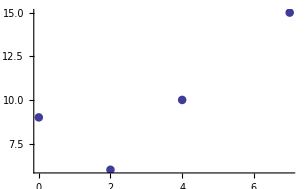
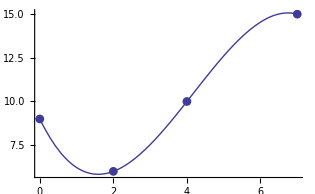
## Interpolar es calcular una función que cumple exactamente unos datos. Datos -Graphics-Función interpolando -Graphics- Un problema de interpolación está formado por unos datos y unas funciones para interpolar. Polinomios: Con frecuencia interpolamos con polinomios, pues los polinomios son las funciones más sencillas para evaluar, derivar, integrar, resolver ecuaciones, etc. ℙ_n={polinomios de grado menor o igual a n} = {a_0+a_1x+...+a_nx^n/ a_0, ..., a_n ∈ ℝ} = <1, x, x^2, ..., x^n> Unisolvencia. Aquellos problemas de interpolación donde existe una única función que interpola se llaman unisolventes. Ejemplos: a) Problema de interpolación: Datos={f(x_0), f(x_1), f(x_2)} Funciones ℙ_2 Un polinomio de grado menor o igual a dos es de la forma p(x) = a+bx+cx^2. Imponiendo los datos llegamos al sistema: p(x_0)=a+bx_0+cx_0^2=f(x_0) p(x_1)=a+bx_1+cx_1^2=f(x_1) p(x_2)=a+bx_2+cx_2^2=f(x_2) La matriz de coeficientes de este sistema es (1 | x_0 | x_0^2 1 | x_1 | x_1^2 1 | x_2 | x_2^2) El determinante de esta matriz es: (x_2-x_1)(x_2-x_0)(x_1-x_0) El determinante será distinto de cero si los tres puntos x_0,x_1,x_2 son tres puntos distintos. Si el determinante es distinto de cero, el sistema de ecuaciones tendrá una única solución. Conclusión: si los tres puntos son distintos, el problema es unisolvente. b) Problema de interpolación: Datos={f(x_0), f(x_1), f ’(x_2)} Funciones ℙ_2 Un polinomio de grado menor o igual a dos es de la forma p(x) = a+bx+cx^2. Imponiendo los datos llegamos al sistema: p(x_0)=a+bx_0+cx_0^2=f(x_0) p(x_1)=a+bx_1+cx_1^2=f(x_1) p’(x_2) = b + 2 cx_2=f ’ (x_2) La matriz de coeficientes de este sistema es (1 | x_0 | x_0^2 1 | x_1 | x_1^2 0 | 1 | 2 x_2) El determinante de esta matriz es: (x_0-x_1)(x_0+x_1- 2 x_2) El determinante será distinto de cero si x_0 es distinto de x_1 y si x_2 no es el punto medio de x_0 y x_1. Si el determinante es distinto de cero, el sistema de ecuaciones tendrá una única solución. Conclusión: si x_0 es distinto de x_1 y si x_2 no es el punto medio de x_0 y x_1, el problema es unisolvente. Por ejemplo, si los datos fuesen f(0), f ’(1) y f(2), el problema no sería unisolvente. En este caso, y según los valores de los datos, o no hay solución o hay infinitas. No basta con tener el mismo número de datos que de incógnitas para que tengamos un problema unisolvente. Interpolación polinomial: Ejemplos clásicos. Datos: Lagrange (valores de la función en distintos puntos), Taylor (valor de la función y sus derivadas consecutivas hasta cierto orden en un punto), Hermite clásico (valor de la función y la primera derivada en diferentes puntos, Hermite generalizado (valor de la función y de algunas derivadas consecutivas en diferentes puntos), ... Ideas: Coeficientes indeterminados: Escribimos el polinomio en la forma habitual e imponemos las condiciones. Aparece un sistema de ecuaciones lineales que puede ser complicado de resolver a mano. Newton: Empezamos con un dato y calculamos la constante que interpola. En cada paso añadimos un nuevo sumando, que se anula en los datos anteriores, e interpolamos un nuevo dato. Newton-diferencias divididas: El polinomio se escribe siguiendo la idea anterior, pero los coeficientes se calculan por una ley de recurrencia. Lagrange: Se buscan funciones que valgan 1 para un dato y cero para el resto (se llaman funciones de Lagrange). Así el polinomio se escribe directamente multiplicando las funciones de Lagrange por los datos. Las funciones de Lagrange pueden ser complicadas de calcular. Unisolvencia: Los problemas anteriores (datos de Lagrange, Taylor, Hermite clásico y generalizado, con polinomios de ℙ_n) son unisolventes siempre que los puntos sean diferentes y el grado n de los polinomios sea el adecuado, es decir el número de datos debe ser n+1, la dimensión del espacio de polinomios. Esto significa que hay una sola solución. Problemas de oscilaciones: Al interpolar una función en cada vez más puntos podríamos pensar que el polinomio de interpolación estaría cada vez más cerca (función y polinomio coinciden en cada vez más puntos), sin embargo eso no tiene por qué ser así y pueden aparecer problemas de oscilaciones entre dos puntos interpolados. La función de Runge que veremos más adelante nos muestra un ejemplo. Ante estos problemas, si tenemos muchos datos que interpolar, podemos pensar en funciones de grado bajo pero definidas a trozos. Una poligonal sería un ejemplo de este tipo. Funciones splines, más concretamente, funciones polinómicas splines, son funciones definidas en un intervalo, dividido en diferentes subintervalos, en cada uno de los cuales la función es un polinomio de hasta cierto grado. En los puntos de unión de dos subintervalos, los polinomios pueden unir con más o menos regularidad. Si unen sólo con continuidad se dice que son de clase 0, si tienen también la misma derivada (la misma recta tangente) se dice que es clase 1, sucesivamente, si la unión se produce con continuidad de hasta la derivada k-ésima en cada punto de unión de los subintervalos, se dice que el spline es de clase k. S_n^k (x_0,x_1, x_2,..., x_m) son las funciones splines de grado n y clase k con nodos x_0,x_1, x_2,..., x_m. Son funciones que en cada intervalo [x_0,x_1], [x_1, x_2],..., [x_(m-1), x_m] son polinomios de grado menor o igual a n y que en cada punto x_1, x_2,..., x_(m-1) la función tiene continuidad tanto de la función como de las derivadas primera, segunda, hasta la k-ésima. Interpolación spline. Con funciones splines podemos plantear muy variados tipos de problemas de interpolación. Ahora podemos cambiar no sólo el tipo de datos o el grado de los polinomios, además podemos cambiar la regularidad o clase de las funciones splines o los nodos. En cada situación habría que estudiar la unisolvencia o la forma de calcular la función spline. Ejemplos de problemas de interpolación unisolventes con funciones splines: Valores de una función en diferentes puntos, x_0,x_1, x_2,..., x_m , funciones splines S_1^0 (x_0,x_1, x_2,..., x_m), se trataría de calcular la poligonal que interpola los diferentes datos. El problema es unisolvente y se puede calcular el spline trabajando en cada uno de los subintervalos y obteniendo la recta que interpola los dos datos que hay en cada subintervalo. Valores de una función y su primera derivada en diferentes puntos, x_0,x_1, x_2,..., x_m con funciones splines S_3^1 (x_0,x_1, x_2,..., x_m). De nuevo es un problema unisolvente. Para obtener el spline interpolador, en cada subintervalo obtenemos el polinomio de grado menor o igual a tres que interpola a la función y la derivada en los dos puntos. Valores de una función en diferentes puntos, x_0,x_1, x_2,..., x_m , funciones splines S_3^2 (x_0,x_1, x_2,..., x_m), añadiendo derivada segunda igual a cero en los extremos. Se trata del spline cúbico natural. Es un problema unisolvente, pero no se puede calcular el spline, trozo a trozo, es necesario calcularlo globalmente, es decir, hay que plantear el sistema de ecuaciones lineales con todos los polinomios. Valores de una función en diferentes puntos, x_0,x_1, x_2,..., x_m , y de la primera derivada en los extremos x_0,x_m, con funciones splines S_3^2 (x_0,x_1, x_2,..., x_m). Se trata del spline cúbico sujeto. De nuevo, es un problema unisolvente, pero no se puede calcular el spline, trozo a trozo, es necesario calcularlo globalmente, es decir, hay que plantear el sistema de ecuaciones lineales con todos los polinomios. Trabajando con splines A la hora de trabajar con las funciones splines podríamos escribir un polinomio en cada subintervalo con sus coeficientes indeterminados e imponer las condiciones de interpolación que haya en cada subintervalo y las condiciones de regularidad que debe tener el spline (continuidad de la función y de las derivadas hasta cierto orden). De esta forma se llega a un sistema de ecuaciones lineales, que al resolverlo nos daría la solución. En ocasiones, el sistema anterior podría tener muchas ecuaciones, por ello puede ser interesante considerar una base de las funciones splines y simplificar el número de ecuaciones e incógnitas del sistema. Base de las funciones splines. S_n^k (x_0,x_1, x_2,..., x_m) =<1,x,x^2, x^3, ..., x^n, (x -x_1)_+^(k+1), ..., (x -x_1)_+^n, (x -x_2)_+^(k+1), ..., (x -x_2)_+^n, ..., (x -x_(m-1))_+^(k+1), ..., (x -x_(m-1))_+^n> donde (x -a)_+^r={0 | x≤ a (x -a)^r | x≥a Error del polinomio de Taylor Si f es una función derivable n+1 veces en el intervalo [x_0,x] tenemos que la diferencia entre f(x) y el polinomio de Taylor de grado n de la función f en el punto x_0 es f(x)-p_n(x) = f^(n+1))(c) (x -x_0)^(n+1) (1/(n+1)!), donde c es un punto entre x_0 y x. Ejemplo. Si f(x)= cos x y obtenemos el polinomio de Taylor de f(x) en el punto 0, interpolando hasta la derivada cuarta, obtenemos p_4(x) = 1 - x^2/2 + x^4/24. La diferencia entre el coseno de 0.2 radianes y el valor de p_4(0.2)=14701/15000≃ 0.98006666 se puede acotar por | cos 0.2 - p_4(0.2) | = |- sen c (0.2 -0)^(4+1) (1/(4+1)!)| ⩽ 0.2^5/120 = 1/375000≃ 0.0000026666 También se podría plantear el problema de encontrar hasta qué derivada debemos interpolar para conseguir que el error sea menor que una cantidad dada. Ejemplo. Si f(x)= sen x y tratamos de aproximar sen 1, podemos buscar un polinomio de Taylor de f(x) en el punto 0, con el grado adecuado para que el error sea menor que 10^-4. Como el error sería |sen 1 -p_n(1)| = |f^(n+1))(c) (1 -0)^(n+1) (1/(n+1)!)| ⩽ 1/(n+1)! ⩽ 10^-4. Para ello es necesario que (n+1)! ≥ 10^4. Esto se consigue con n=7, pues (7+1)!=8!=40320. Ahora calculamos el polinomio para n=7, p_7(x) = 0+ 1 x/1 - 0x^2/2 - 1 x^3/6+ 0 x^4/24 + 1 x^5/120 - 0 x^6/720 - 1 x^7/5040 = x - x^3/6 + x^5/120 - x^7/5040. En el punto 1, p_7(1) = 1 - 1/6 + 1/120 - 1/5040 = 4241/5040 ≃ 0.8414682540. La diferencia con el valor del sen 1 es 2.7308 10^-6. Claramente es menor que el error máximo permitido en el problema. Aproximación por mínimos cuadrados En ocasiones, los datos de una función provienen de mediciones que están sujetas a errores, y aunque sepamos que la función debe ser de un determinado tipo, los datos no corresponden a ninguna de ellas. Por ejemplo, podemos saber que una función debe ser lineal, es decir del tipo f(x) = a + bx, por tanto, una combinación lineal de las funciones 1 y x, pero los datos medidos (x_i, y_i) pueden no estar alineados y no estar en la gráfica de ninguna recta. Para intentar paliar los efectos de los errores en las mediciones, o las alteraciones en los datos por el “ruido”, podemos buscar la combinación lineal que esté más próxima a los datos. Para hacer esto hay que medir una “distancia” entre funciones. Necesitamos definir qué entendemos por cercanía. Supongamos que conocemos unos valores (x_i,y_i), i=0,...,m, y buscamos una función que los aproxime en cierto subespacio vectorial de funciones. La diferencia |p(x_i)-y_i| sería el error que la función p tiene en el dato i-ésimo. A partir del error en un punto tenemos que dar una idea de la cercanía entre la función de partida y la función p. Algunas posibilidades son: 1) Máx |p(x_i)-y_i| (aproximación uniforme) 2) ∑_(i=0)^m |p(x_i)-y_i| 3) (∑_(i=0)^m |p(x_i)-y_i|)^2 (error cuadrático) 4) (∑_(i=0)^m |p(x_i)-y_i|)^4 (o con otro exponente) Es posible dar diferentes pesos a los errores en los distintos puntos, por ejemplo ∑_(i=0)^m (w_i(p(x_i)-y_i))^2. La forma más usual (y sencilla) de buscar la función más cercana es con la suma de las diferencias (o errores) elevadas al cuadrado. Se habla entonces de aproximación por mínimos cuadrados. Es decir, se trata de buscar la función p que hace mínima la expresión ∑_(i=0)^m (p(x_i)-y_i)^2, dentro de un cierto subespacio vectorial. Así, si consideramos los polinomios de grado menor o igual a uno, hablaríamos de la recta que mejor aproxima en el sentido de los mínimos cuadrados (recta de mínimos cuadrados). Pero pueden considerarse otras funciones, polinomios hasta cierto grado, u otros espacios de funciones. Para calcular la recta de mínimos cuadrados podemos considerar la expresión del error cuadrático como una función de los coeficientes del polinomio. Sea p(x)=a+bx, entonces la función del error es Error[a,b]=∑_(i=0)^m (a+b x_i-y_i)^2 y para minimizar la expresión del error cuadrático hacemos las derivadas parciales respecto a las variables a y b, e igualamos a cero. Llegamos así a un sistema de ecuaciones lineales de dos ecuaciones con dos incógnitas. El sistema, puede demostrarse, que tiene solución única y que corresponde con el mínimo. (∂ Error[a,b])/(∂ a)=0 (∂ Error[a,b])/(∂ b)=0} ⇒ {a (m+1)+b∑_(i=0)^m x_i = ∑_(i=0)^m y_i a∑_(i=0)^m x_i + b∑_(i=0)^m x_i^2= ∑_(i=0)^m y_i x_i son las llamadas ecuaciones normales

## Ejemplo 1. PROBLEMA DE INTERPOLACIÓN DE LAGRANGE

Calcular el polinomio de grado menor o igual a 3 que interpola los datos: f(0)=9, f(2)=6, f(4)=10, f(7)=15.
Solución: Es un problema de interpolación polinomial con 4 datos lagrangianos (o de Lagrange) con polinomios de grado menor o igual a 3. Es un problema unisolvente (significa que hay una única solución).

Los datos podemos ponerlos en una lista, separados por llaves y comas. Con la función ListPlot podemos dibujar los puntos de la lista y con la opción PlotStyle->PointSize [XX] podemos cambiar el tamaño de los puntos para verlos como más nos convenga. Si le damos un nombre (por ejemplo, puntos) podemos utilizar el dibujo cuando lo necesitemos.

```mathematica
datos= {{0,9},{2,6},{4,10},{7,15}}
```

{{0,9},{2,6},{4,10},{7,15}}

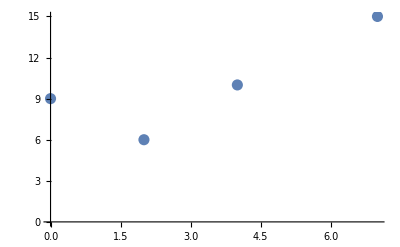

```mathematica
puntos=ListPlot[datos,PlotStyle->PointSize[0.02]]
```

Método de solución: Coeficientes indeterminados.

El polinomio se escribe en la forma habitual y escribimos todas las condiciones que dan los datos. Para escribir el polinomio con el Mathematica escogemos un nombre (por ejemplo, p) y definimos la función (Recordemos: corchetes [ ], guión bajo _ , dos puntos : )

```mathematica
p[x_]:=a + b x + c x^2 + d x^3
```

Imponemos las condiciones, lo que nos lleva a un sistema de ecuaciones lineales y que resolvemos con Solve. Por un lado ponemos las ecuaciones (cuidado: doble igual) separadas por comas y agrupadas entre llaves { }, por otro ponemos las incógnitas, también separadas por comas y entre llaves.

```mathematica
Solve[{p[0]==9,p[2]==6,p[4]==10,p[7]==15},{a,b,c,d}]
```

{{a→9,b→-1817/420,c→471/280,d→-113/840}}

Para sustituir esos valores en el polinomio podemos utilizar la instrucción p[x]/.% . El símbolo % se refiere a lo último que haya calculado el Mathematica. Cuidado: lo último calculado, no lo que aparece en la línea superior, o cualquier otra cosa. Los símbolos /. son las instrucciones para la sustitución. Sin embargo, el polinomio continúa con su valor inicial, es sólo para ver cómo quedaría si hiciésemos el cambio.

```mathematica
p[x]/.%
```

{9-(1817 x)/420+(471 x^2)/280-(113 x^3)/840}

Con la instrucción Plot podemos dibujar el polinomio interpolador. Primero se escribe la expresión de la función (que podemos simplificar copiando el resultado de la sustitución anterior y pegándola en la instrucción Plot) y después ponemos la variable y los extremos del intervalo donde queremos ver la gráfica (todo esto entre llaves { } ). Podemos darle un nombre (por ejemplo, polinomio). Si escribimos punto y coma ";" , después de la instrucción Plot, el dibujo no aparecerá.

```mathematica
polinomio=Plot[9-(1817 x)/420+(471 x^2)/280-(113 x^3)/840,{x,0,7}];
```

Para ver las dos gráficas juntas (la de los puntos y la del polinomio) utilizamos la instrucción Show y escribimos los nombres que les hemos dado a las gráficas ("puntos" y "polinomio"). De esta manera podemos comprobar si el polinomio calculado realmente interpola los datos.

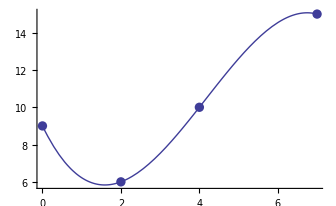

```mathematica
Show[puntos,polinomio]
```

Por tanto, el polinomio calculado 9-(1817 x)/420+(471 x^2)/280-(113 x^3)/840 es el que interpola los datos.

Método de solución: Idea de Newton.

En este método ordenamos los datos (para datos lagrangianos el orden no importa) y progresivamente interpolamos en cada paso un dato más aumentando el grado del polinomio pero aprovechando lo que hemos conseguido en el paso anterior.
 
Comenzamos con una constante para interpolar el primer dato.

```mathematica
q[x_]:=a
```

```mathematica
Solve[q[0]==9,a]
```

{{a→9}}

Al polinomio constante calculado le añadimos un polinomio de grado uno que se anule en el punto anterior.

```mathematica
q[x_] := 9 + b (x - 0)
```

```mathematica
Solve[q[2]==6,b]
```

{{b→-3/2}}

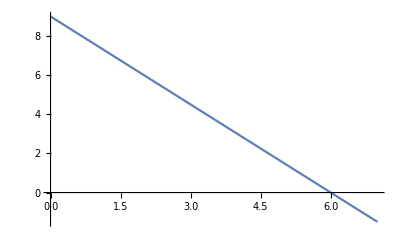

```mathematica
pol2=Plot[9-3/2 x,{x,0,7}]
```

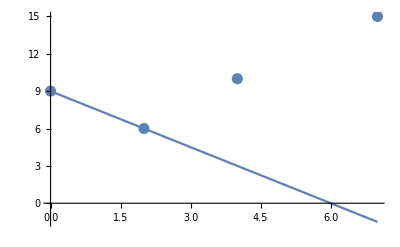

```mathematica
Show[pol2,puntos,PlotRange->All]
```

Al polinomio calculado le añadimos un polinomio de grado dos que se anule en los dos puntos anteriores.

```mathematica
q[x_]:=9-3/2 x + c (x-0)(x-2)
```

```mathematica
Solve[q[4]==10,c]
```

{{c→7/8}}

```mathematica
pol3=Plot[9-3/2 x+7/8 (x-0)(x-2),{x,0,7}];
```

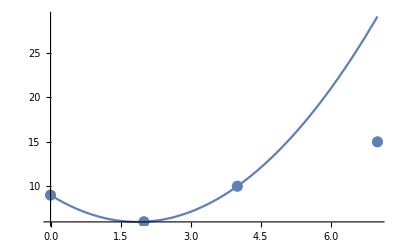

```mathematica
Show[pol3,puntos,PlotRange->All]
```

Al polinomio calculado le añadimos un polinomio de grado tres que se anule en los tres puntos anteriores.

```mathematica
q[x_]:=9-3/2 x+7/8 (x-0)(x-2)+d (x-0)(x-2)(x-4)
```

```mathematica
Solve[q[7]==15,d]
```

{{d→-113/840}}

```mathematica
pol4=Plot[9-3/2 x+7/8 (x-0)(x-2)-113/840 (x-0)(x-2)(x-4),{x,0,7}];
```

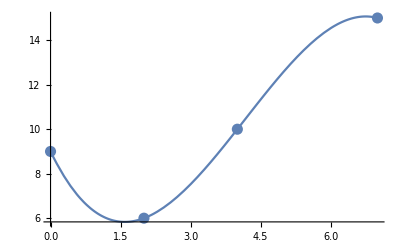

```mathematica
Show[pol4,puntos,PlotRange->All]
```

El polinomio interpolador es 9-3/2 x+7/8 (x-0)(x-2)-113/840 (x-0)(x-2)(x-4). Se trata del mismo polinomio que antes pero escrito de otra forma, en otra base. En la práctica escribiríamos el polinomio en la forma de Newton y resolveríamos en un sólo sistema. Es decir, q[x_]:=a + b (x-0)+c(x-0)(x-2)+d(x-0)(x-2)(x-4) e impondríamos las condiciones de interpolar en los cuatro puntos, es decir Solve[{q[0]==9,q[2]==6,q[4]==10,q[7]==15},{a,b,c,d}] Es otro sistema de 4 ecuaciones con cuatro incógnitas, pero mucho más fácil de resolver pues es triangular. Para resolver a mano es mucho más fácil.

Método: Newton con diferencias divididas.

Se trata de escribir el polinomio en la forma de Newton, pero calcular los coeficientes mediante un algoritmo que llamamos de diferencias divididas.

Comenzamos con los datos y escribimos
f[0]=f(0)
f[2]=f(2)
f[4]=f(4)
f[7]=f(7)
Ahora calculamos
f[0,2]=(f[2]-f[0])/(2-0)
f[2,4]=(f[4]-f[2])/(4-2)
f[4,7]=(f[7]-f[4])/(7-4)
Ahora diferencias divididas con 3 puntos.
f[0,2,4]=(f[2,4]-f[0,2])/(4-0)
f[2,4,7]=(f[4,7]-f[2,4])/(7-2)
Finalmente la diferencia dividida de los 4 puntos
f[0,2,4,7]=(f[2,4,7]-f[0,2,4])/(7-0)
El polinomio se escribe como
f[0] + f[0,2] (x-0) + f[0,2,4] (x-0)(x-2) + f[0,2,4,7] (x-0)(x-2)(x-4)

Método: Idea de Lagrange

Se trata de buscar funciones que valgan 1 para un dato y cero para los demas.
Por ejemplo, para nuestros datos tenemos que calcular las cuatro funciones de Lagrange:

```mathematica
L0[x_]:=((x-2)(x-4)(x-7))/((0-2)(0-4)(0-7))
```

```mathematica
L2[x_]:=((x-0)(x-4)(x-7))/((2-0)(2-4)(2-7))
```

```mathematica
L4[x_]:=((x-0)(x-2)(x-7))/((4-0)(4-2)(4-7))
```

```mathematica
L7[x_]:=((x-0)(x-2)(x-4))/((7-0)(7-2)(7-4))
```

Ahora el polinomio interpolador es muy fácil de calcular pues basta sumar las funciones anteriores multiplicadas por el dato correspondiente
f(0) L0(x)+f(2)L2(x)+f(4)L4(x)+f(7)L7(x)

```mathematica
9L0[x]+6L2[x]+10L4[x]+15L7[x]
```

-9/56 (-7+x) (-4+x) (-2+x)+3/10 (-7+x) (-4+x) x-5/12 (-7+x) (-2+x) x+1/7 (-4+x) (-2+x) x

Vuelve a ser el mismo polinomio escrito de otra forma.

```mathematica
9L0[x]+6L2[x]+10L4[x]+15L7[x]//Simplify
```

1/840 (7560-3634 x+1413 x^2-113 x^3)

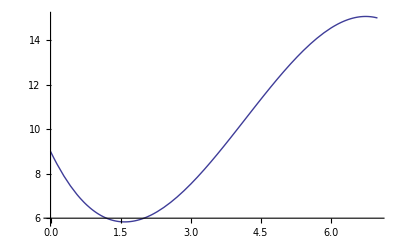

```mathematica
polilagrange=Plot[1/840 (7560-3634 x+1413 x^2-113 x^3),{x,0,7}]
```

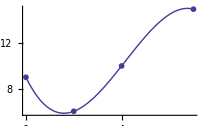

```mathematica
Show[puntos,polilagrange]
```

## Ejemplo 2. INTERPOLACIÓN DE TAYLOR

Calcular el polinomio de grado menor o igual a 3 que interpola los datos: 
		f (2)=3, f ' (2)=6, f ''(2)=-3, f '''(2)=4.
Solución: Es un problema de interpolación polinomial con 4 datos de Taylor (valor de la función junto con las derivadas consecutivas hasta la tercera en un punto) con polinomios de grado menor o igual a 3. Es un problema unisolvente (significa que hay una única solución). 

El cálculo del polinomio de Taylor podríamos hacerlo de diversas formas: 

1) Coeficientes Indeterminados. 

Para ello, escribimos el polinomio en la forma usual, imponemos las condiciones y resolvemos el sistema

```mathematica
p[x_]:= a + b x + c x^2+ d x^3
```

```mathematica
Solve[{p[2]==3,p'[2]==6,p''[2]==-3,p'''[2]==4},{a,b,c,d}]
```

{{a→-61/3,b→20,c→-11/2,d→2/3}}

```mathematica
p[x]/.%
```

{-61/3+20 x-(11 x^2)/2+(2 x^3)/3}

El polinomio que buscamos es -61/3+20 x-(11 x^2)/2+(2 x^3)/3

2) Idea de Newton. 

Se empieza con un dato y una constante, p(x)=a, después se añaden nuevos sumandos al polinomio y se van considerando nuevos datos. Los sumandos que pongamos no deben "estropear" lo conseguido, es decir, deben anularse en los datos anteriores. 
Como el primer dato es el valor en 2, el primer sumando que añadimos debe ser b(x-2). La b la calculamos con el segundo dato, f '(2). El siguiente sumando debe anularse en el 2 y también su derivada por ello añadimos c (x-2)^2. La c se calcula con el dato de la derivada segunda en 2. Finalmente, añadimos d (x-2)^3, pues este sumando se anula en el punto 2, así como la primera y segunda derivada en 2. Así, en este caso el polinomio se escribirá como:
a + b (x-2) + c (x-2)^2+ d (x-2)^3

```mathematica
p[x_]:= a + b (x-2) + c (x-2)^2+ d (x-2)^3
```

Escrito así, el sistema de ecuaciones que hay que resolver es mucho más sencillo.

```mathematica
p[2]==3
```

a==3

```mathematica
p'[2]==6
```

b==6

```mathematica
p''[2]==-3
```

2 c==-3

```mathematica
p'''[2]==4
```

6 d==4

```mathematica
Solve[{p[2]==3,p'[2]==6,p''[2]==-3,p'''[2]==4},{a,b,c,d}]
```

{{a→3,b→6,c→-3/2,d→2/3}}

```mathematica
p[x]/.%
```

{3+6 (-2+x)-3/2 (-2+x)^2+2/3 (-2+x)^3}

El polinomio de interpolación escrito en la forma de Newton es 3+6 (-2+x)-3/2 (-2+x)^2+2/3 (-2+x)^3. Si desarrollamos las potencias encontraríamos el mismo polinomio que calculamos por coeficientes indeterminados.

3) Idea de Lagrange. 

Se trata de buscar funciones que valgan 1 para un dato y cero para los demás.

En este caso las cuatro funciones son:

1, (x-2), (x-2)^2/2, (x-2)^3/(3!)

el polinomio se escribirá entonces multiplicando las funciones de Lagrange por los datos. Es decir,

3+6 (x-2)-3 (x-2)^2/2+6 (x-2)^3/(3!)

## Ejemplo 3. INTERPOLACIÓN DE TAYLOR DE UNA FUNCIÓN CONOCIDA

Dada una función derivable podemos calcular los polinomios de Taylor e ir comparando la función con los sucesivos polinomios cada vez de mayor grado.
Algunas funciones como la exponencial, el logaritmo, el seno, el coseno, etc. son conocidas con total exactitud en un punto, al igual que sus sucesivas derivadas. En cambio, en el resto de los puntos podemos tener problemas para conocer su valor o su derivada (pensad que no hubiese calculadoras). El polinomio de Taylor permitiría tener un valor aproximado en otros puntos, pues para evaluar el polinomio basta sumar, restar o multiplicar.

```mathematica
f[x_]:=E^x
```

```mathematica
a=0
```

0

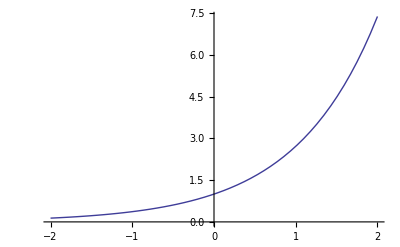

```mathematica
gf=Plot[f[x],{x,a-2,a+2}]
```

```mathematica
p0[x_]:=f[a]
```

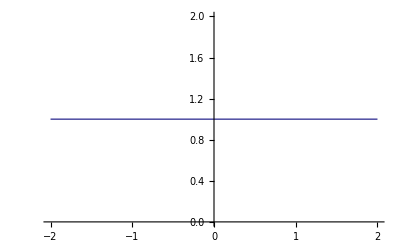

```mathematica
gf0=Plot[p0[x],{x,a-2,a+2}]
```

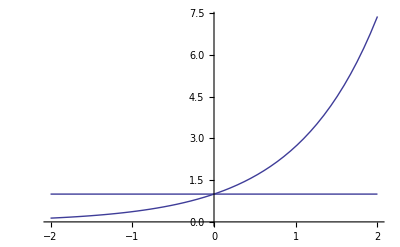

```mathematica
Show[gf,gf0]
```

```mathematica
p1[x_]:=f[a]+f'[a] (x-a)
```

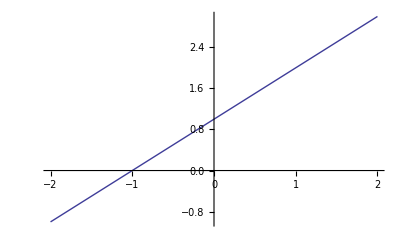

```mathematica
gf1=Plot[p1[x],{x,a-2,a+2}]
```

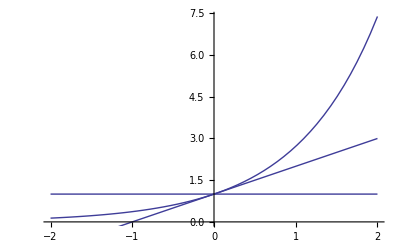

```mathematica
Show[gf,gf0,gf1]
```

```mathematica
p2[x_]:=f[a]+f'[a] (x-a) + f''[a] (x-a)^2/(2!)
```

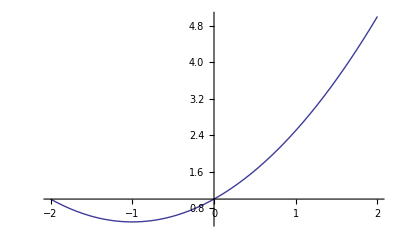

```mathematica
gf2=Plot[p2[x],{x,a-2,a+2}]
```

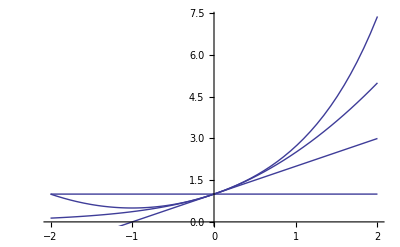

```mathematica
Show[gf,gf0,gf1,gf2]
```

Observamos cómo los sucesivos polinomios están "cerca" de la función en un intervalo cada vez más amplio.

Así podemos seguir añadiendo un sumando en cada paso.

```mathematica
p3[x_]:=p2[x]+f'''[a](x-a)^3/(3!)
```

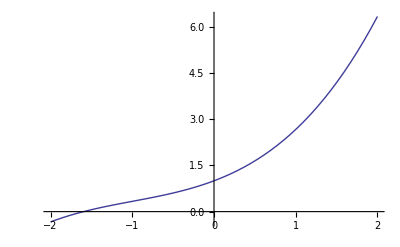

```mathematica
gf3=Plot[p3[x],{x,a-2,a+2}]
```

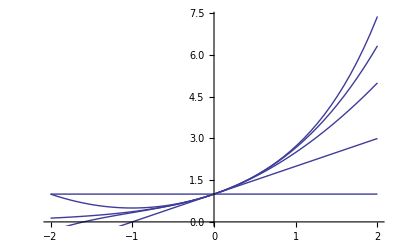

```mathematica
Show[gf,gf0,gf1,gf2,gf3]
```

Si quisiéramos calcular uno de mayor grado vemos que es algo tedioso escribir los sumandos y poner las "comillas" para las derivadas.

```mathematica
p6[x_]:=f[a]+f'[a] (x-a) + f''[a](x-a)^2/2+f'''[a](x-a)^3/(3!)+f''''[a](x-a)^4/(4!)+f'''''[a](x-a)^5/(5!)+f''''''[a](x-a)^6/(6!)
```

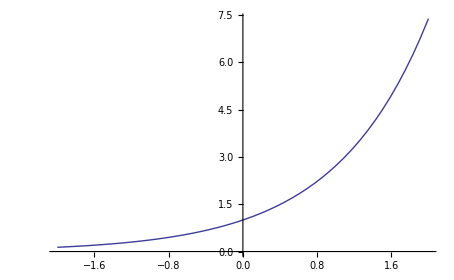

```mathematica
Plot[{f[x],p6[x]},{x,a-2,a+2}]
```

Podemos también comprobar lo bueno de la aproximación en base a comparar los valores de la función y del polinomio.

```mathematica
f[a+2.5]
```

12.1825

```mathematica
p6[a+2.5]
```

12.0097

```mathematica
f[a+2.5]-p6[a+2.5]
```

0.172837

Si los puntos están más cerca del punto donde evaluamos la función y derivadas el error suele ser menor.

```mathematica
f[a+1.3]-p6[a+1.3]
```

0.00148085

Para calcular el polinomio de Taylor de cualquier grado necesitaríamos hacer uso de la función derivada D. También deberíamos usar la notación de sumatoria para tener la fórmula escrita pra cualquier grado. La derivada i-ésima de la función f[x] sería D[f[x],{x,i}]. Sin embargo, si x va a ser variable independiente del polinomio de Taylor y lo vamos a concretar para i

```mathematica
Taylor[n_,x_]:=∑_(i=0)^n (D[f[y],{y,i}]/.{y->a})(x-a)^i/(i!)
```

```mathematica
Taylor[5,x]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

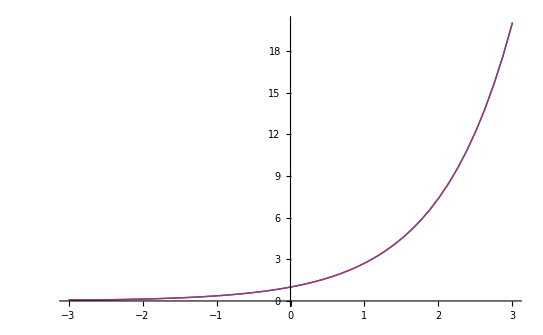

```mathematica
Plot[{f[x],Taylor[8,x]},{x,a-3,a+3}]
```

En este caso, con el polinomio de grado 8, entre -3 y 3, vemos que las dos gráficas se superponen y no podemos distinguirlas.

```mathematica
Taylor[8,x]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320

Si aumentamos el grado podemos incluso evaluar en puntos más lejanos y conseguir buenas aproximaciones.

```mathematica
Taylor[20,5.5]
```

244.692

```mathematica
f[5.5]-Taylor[20,5.5]
```

0.0000916728

En este caso el polinomio de grado 20 y la función se diferencian en el punto 5.5 menos de una diezmilésima.

Podemos cambiar la función y el punto.

```mathematica
f[x_]:=Log[x]
```

```mathematica
a=1
```

1

```mathematica
Taylor[n_,x_]:=∑_(i=0)^n (D[f[y],{y,i}]/.{y->a})(x-a)^i/(i!)
```

```mathematica
Taylor[8,x]
```

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5-1/6 (-1+x)^6+1/7 (-1+x)^7-1/8 (-1+x)^8+x

```mathematica
Expand[%]
```

-761/280+8 x-14 x^2+(56 x^3)/3-(35 x^4)/2+(56 x^5)/5-(14 x^6)/3+(8 x^7)/7-x^8/8

Con la instrucción Expand se desarrollan las potencias y el polinomio aparece en una forma usual.

```mathematica
Taylor[20,1.5]
```

0.405465

```mathematica
Log[1.5]
```

0.405465

```mathematica
Taylor[20,1.5]-Log[1.5]
```

-1.5374×10^-8

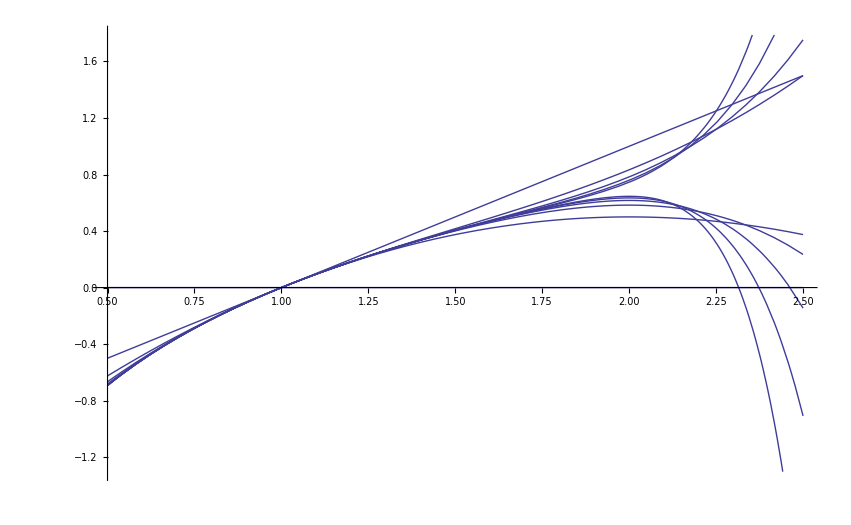

```mathematica
Plot[Table[Taylor[n,x],{n,0,10}],{x,0.5,2.5}]
```

La instrucción Table[Taylor[n, x], {n, 0, 10}] crea una Lista con los polinomios de Taylor desde grado 0 a grado 10. Al introducirla en la orden Plot, se dibujan simultáneamente todos los polinomios.

## Ejemplo 4. INTERPOLACIÓN DE HERMITE

Calcular el polinomio de grado menor o igual a 3 que interpola los datos:
	   f (4) = 3, f ' (4) = 1, f (7) = -3, f ' (7) = -4.
Solución : Es un problema de interpolación polinomial con 4 datos de Hermite (valor de la función y de la primera derivada en dos puntos distintos) con polinomios de grado menor o igual a 3. Es un problema unisolvente (significa que hay una única solución). El cálculo del polinomio de Hermite podríamos hacerlo de diversas formas:
  
1) Coeficientes indeterminados. Para ello, escribimos el polinomio en la forma usual, imponemos las condiciones y resolvemos el sistema

```mathematica
p[x_]:= a + b x + c x^2+ d x^3
```

```mathematica
Solve[{p[4]==3,p'[4]==1,p[7]==-3,p'[7]==-4},{a,b,c,d}]
```

{{a→-265/9,b→17,c→-8/3,d→1/9}}

```mathematica
p[x]/.%
```

{-265/9+17 x-(8 x^2)/3+x^3/9}

El polinomio que buscamos es -265/9+17 x-(8 x^2)/3+x^3/9. Para encontrar estos coeficientes ha sido necesario resolver un sistema de cuatro ecuaciones con cuatro incógnitas. Para que resulte más fácil podemos utilizar las ideas de Newton o Lagrange

2) Idea de Newton: El polinomio se escribe ahora de forma que el segundo sumando se anule en el primer dato, el tercer sumando en el primero y segundo datos, y finalmente, el cuarto sumando se anule en los tres primeros datos:

p(x)=a + b (x-4) + c (x-4)^2+ d (x-4)^2(x-7)

De esta forma el sistema es mucho más fácil de resolver:

```mathematica
p[x_]:= a + b (x-4) + c (x-4)^2+ d (x-4)^2(x-7)
```

```mathematica
{p[4]==3,p'[4]==1,p[7]==-3,p'[7]==-4}
```

{a==3,b==1,a+3 b+9 c==-3,b+6 c+9 d==-4}

Vemos como la primera ecuación es simplemente a=3. La segunda es b=1. La tercera ecuación permite encontrar c (sabiendo a y b). Finalmente, encontraríamos d de la última ecuación, usando los valores calculados de a, b y c.

```mathematica
Solve[{p[4]==3,p'[4]==1,p[7]==-3,p'[7]==-4},{a,b,c,d}]
```

{{a→3,b→1,c→-1,d→1/9}}

El polinomio que buscamos es 3+(x-4)-(x-4)^2+1/9  (x-4)^2(x-7). Aunque está escrito en otra base, es el mismo que antes calculamos.

Método: Newton con diferencias divididas.

Se trata de escribir el polinomio en la forma de Newton, pero calcular los coeficientes mediante el algoritmo de diferencias divididas con la adaptación para usar datos de derivadas. La diferencia dividida con puntos repetidos n+1 veces es f[x_0,x_0,x_0,...,x_0] = f^(n)) (x_0) /(n!).

Comenzamos con los datos y escribimos:
f[4]=f(4)
f[4]=f(4)
f[7]=f(7)
f[7]=f(7)
Esto sería la primera columna, repitiendo los puntos tantas veces como orden hasta el que llegue la derivada.

En la segunda columna colocamos la información de la derivada
f[4,4]=f '(4)
f[7,7]=f '(7)
Ahora calculamos el resto de coeficientes como hacíamos para la tabla de diferencias divididas en los datos lagrangianos.
f[4,7]=(f[7]-f[4])/(7-4)
Ahora diferencias divididas con 3 puntos.
f[4,4,7]=(f[4,7]-f[4,4])/(7-4)
f[4,7,7]=(f[7,7]-f[4,7])/(7-4)
Finalmente la diferencia dividida de los 4 puntos
f[4,4,7,7]=(f[4,7,7]-f[4,47])/(7-4)
El polinomio se escribe como
f[4] + f[4,4] (x-4) + f[4,4,7] (x-4)^2 + f[4,4,7,7] (x-4)^2(x-7)

También se puede usar la idea de Lagrange, aunque obtener las funciones de Lagrange no es tan inmediato como.

## Más ejemplos

Con el Mathematica podemos calcular polinomios de interpolación para diversos tipos de datos. Usamos la instrucción InterpolatingPolynomial.

#### Interpolar valores de la función

Un primer tipo es el de datos lagrangianos (valores de la función en varios puntos).

Ejemplo. Calcular el polinomio de grado menor o igual a 3 que interpola los datos f(0)=1, f(1)=3, f(2)=7, f(5)=8.

```mathematica
puntos=ListPlot[{{0,1},{1,3},{2,7},{5,8}},PlotStyle->PointSize[0.02]]
```

-Graphics-

```mathematica
InterpolatingPolynomial[{{0,1},{1,3},{2,7},{5,8}},x]
```

1+(2+(1-23/60 (-2+x)) (-1+x)) x

```mathematica
Collect[%,x]
```

1+(7 x)/30+(43 x^2)/20-(23 x^3)/60

Solución: El polinomio de interpolación pedido es 1+(7 x)/30+(43 x^2)/20-(23 x^3)/60.

Observaciones: 
a) El polinomio interpolador aparece escrito en la forma de Newton, no en potencias de x, y preparado para usar el algoritmo de Horner. En esta forma, evaluar el polinomio requiere de menos operaciones.
b) Si queremos tener escrito en la forma habitual, podemos pedirle la Mathematica que simplifique (con Simplify ) o que agrupe en potencias (con Collect). 
c) Para comprobar podemos evaluar el polinomio en los puntos de interpolación. También podríamos dibujar el polinomio y ver si pasa por los puntos esperados.

```mathematica
p[x_]:=1+(7 x)/30+(43 x^2)/20-(23 x^3)/60
```

```mathematica
{p[0],p[1],p[2],p[5]}
```

{1,3,7,8}

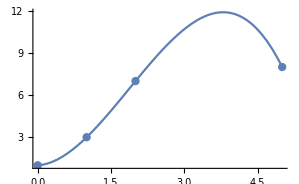

```mathematica
Show[puntos,Plot[p[x],{x,0,5}],PlotRange->All]
```

#### Interpolar valores de la función y la derivada en diferentes puntos

También con la InterpolatingPolynomial podemos interpolar datos de derivadas, comenzando con el valor de la función en un punto y valores de las derivadas sucesivas hasta cierto orden, con la posibilidad de que en cada punto se llegue hasta un orden de derivada diferente. Este tipo de datos se llama de Hermite generalizado.

Por ejemplo, calcular el polinomio que interpola los datos f(0)=1, f ’(0)=1, f’’(0)=0, f(1)=3,f ’(1)=2, f(2)=7, f(5)=8.

```mathematica
InterpolatingPolynomial[{{0,1,1,0},{1,3,2},{2,7},{5,8}},x]
```

1+x (1+(1+(-2+(3/2-(2123 (-2+x))/6000) (-1+x)) (-1+x)) x^2)

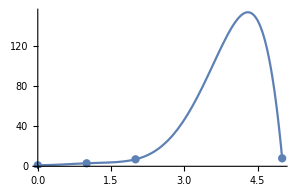

```mathematica
Show[puntos,Plot[1+x (1+(1+(-2+(3/2-(2123 (-2+x))/6000) (-1+x)) (-1+x)) x^2),{x,0,5}],PlotRange->All]
```

#### Interpolación de Taylor: valor de la función y de sus derivadas consecutivas en un punto

Otro tipo de interpolación es el de Taylor. En muchos casos, conocemos una función sólo en un punto, pero también conocemos en ese punto el valor de sus derivadas. Esto ocurre con la función exponencial en el punto 0, con la función seno o coseno en el 0, con la función logaritmo o raíz cuadrada en el punto 1, etc.
Con la información en un punto, intentamos evaluar la función (aunque sea de forma aproximada) en otros puntos.

```mathematica
f[x_]:=ⅇ^x
```

```mathematica
x0=0;
```

```mathematica
P[x_,n_]:=∑_(i=0)^n (D[f[y],{y,i}]/.y->x0)(x-x0)^i/(i!)
```

```mathematica
P[x,6]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720

```mathematica
P[0.23,6]
```

1.2586

```mathematica
f[0.23]
```

1.2586

```mathematica
P[0.23,6]-f[0.23]
```

-6.95491×10^-9

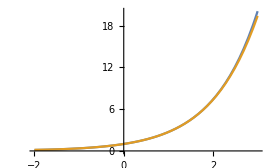

```mathematica
Plot[{f[x],P[x,6]},{x,-2,3}]
```

Los polinomios y la función están muy “cerca”. Por ello, podríamos evaluar el polinomio y tener una buena aproximación de la función exponencial. La aproximación es mejor cuanto más cerca estemos del punto 0 y cuantas más derivadas utilicemos.

Veamos algún otro ejemplo.

```mathematica
f[x_]:=Cos[x]
```

```mathematica
x0=0;
```

```mathematica
P[x_,n_]:=∑_(i=0)^n (D[f[y],{y,i}]/.y->x0)(x-x0)^i/(i!)
```

```mathematica
P[x,6]
```

1-x^2/2+x^4/24-x^6/720

```mathematica
P[0.23,6]
```

0.973666

```mathematica
f[0.23]
```

0.973666

```mathematica
P[0.23,6]-f[0.23]
```

-1.9411×10^-10

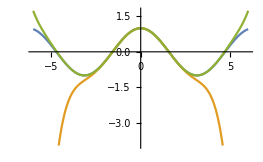

```mathematica
Plot[{f[x],P[x,6],P[x,12]},{x,-6,6}]
```

La gráfica del polinomio de grado 6 parece que se “separa” de la gráfica del coseno después del 2, la del polinomio de grado 12 se “separa” después del 4.

```mathematica
f[x_]:=√x
```

```mathematica
x0=1;
```

```mathematica
P[x_,n_]:=∑_(i=0)^n (D[f[y],{y,i}]/.y->x0)(x-x0)^i/(i!)
```

```mathematica
P[x,6]//Simplify
```

(231+1386 x-1155 x^2+924 x^3-495 x^4+154 x^5-21 x^6)/1024

```mathematica
P[1.23,6]
```

1.10905

```mathematica
f[1.23]
```

1.10905

```mathematica
P[1.23,6]-f[1.23]
```

-4.62548×10^-7

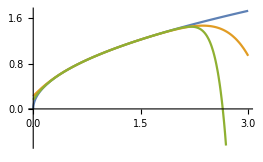

```mathematica
Plot[{f[x],P[x,6],P[x,12]},{x,0,3}]
```

## Interpolación de Taylor para aproximar la solución de una ecuación diferencial

Podríamos utilizar este método para aproximar la solución de problemas de valores iniciales en ecuaciones diferenciales.

Consideremos el problema de valores iniciales:

y’ = y (2 - x y)
y(0)=1

Se trata de buscar una función y(x) que cumpla la ecuación diferencial y la condición inicial.

Si no pudiésemos resolver la ecuación por algunos de los métodos estudiados podríamos buscar el valor de la función y sus derivadas en el cero.

y(0)=1
y’(0)=1(2-0*1)=2

Para las otras derivadas, derivamos en la ecuación diferencial.

y’’ = y’(2-x y) + y (-y-xy’)
Evaluamos en cero
y’’(0)=2(2-0*1)+1(-1-0*2)=3

Sucesivamente podríamos calcular más derivadas en cero y así tener polinomios de Taylor de mayor grado.

## Interpolación en muchos puntos. El ejemplo de Runge.

#### Interpolar la función 1/(1+x^2) en el intervalo [-5,5]. (Sirve para mostrar que la interpolación polinomial no tiene por qué converger a la función interpolada, aunque la función y los polinomios coincidan en "muchos" puntos.)

Podríamos pensar que al aumentar el número de puntos en los que interpolamos una función, la diferencia entre la función interpolada y los polinomios interpoladores disminuye y tiende a anularse. En general, esto no es cierto.

Al aumentar el número de puntos interpolados los polinomios pueden aumentar sus oscilaciones (aunque siempre interpolando todos los datos). Incluso la diferencia (o error de interpolación) podría tender a infinito.

Un ejemplo clásico que podemos encontrar en los libros es el ejemplo de Runge. Consideramos la función f(x)=1/(1+x^2) en intervalo [-5,5] e interpolamos en puntos equidistantes. Al aumentar el número de puntos de interpolación, aparecen grandes oscilaciones y la diferencia entre el polinomio y la función en el intervalo [-5,5] tiende a infinito.

```mathematica
f[x_]:=1/(1+x^2)
```

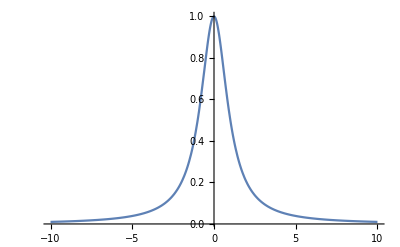

```mathematica
Plot[f[x],{x,-10,10},PlotRange->All]
```

```mathematica
n=20;
```

```mathematica
datos=Table[{-5+10i/n,f[-5+10i/n]},{i,0,n}]
```

{{-5,1/26},{-9/2,4/85},{-4,1/17},{-7/2,4/53},{-3,1/10},{-5/2,4/29},{-2,1/5},{-3/2,4/13},{-1,1/2},{-1/2,4/5},{0,1},{1/2,4/5},{1,1/2},{3/2,4/13},{2,1/5},{5/2,4/29},{3,1/10},{7/2,4/53},{4,1/17},{9/2,4/85},{5,1/26}}

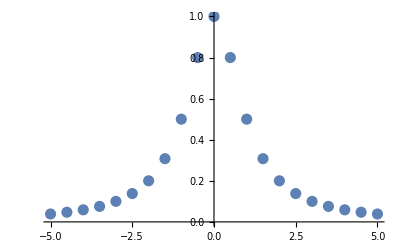

```mathematica
dat=ListPlot[datos ,PlotStyle->PointSize[0.02]]
```

```mathematica
InterpolatingPolynomial[datos,x]//Simplify
```

1/375343085000(375343085000-362483525000 x^2+282766200500 x^4-146995641191 x^6+47388156676 x^8-9426188577 x^10+1164257172 x^12-88735648 x^14+4032128 x^16-99584 x^18+1024 x^20)

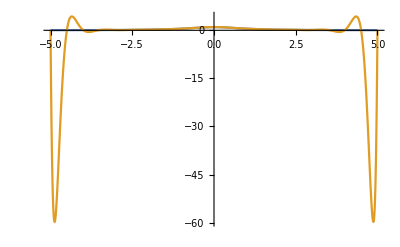

```mathematica
Plot[{f[x],%},{x,-5,5}, PlotRange->All]
```

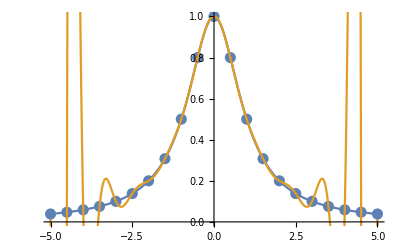

```mathematica
Show[dat, Plot[{f[x],1/375343085000(375343085000-362483525000 x^2+282766200500 x^4-146995641191 x^6+47388156676 x^8-9426188577 x^10+1164257172 x^12-88735648 x^14+4032128 x^16-99584 x^18+1024 x^20)},{x,-5,5}]]
```

```mathematica
n=40;
```

```mathematica
datos=Table[{-5+10i/n,f[-5+10i/n]},{i,0,n}]
```

{{-5,1/26},{-19/4,16/377},{-9/2,4/85},{-17/4,16/305},{-4,1/17},{-15/4,16/241},{-7/2,4/53},{-13/4,16/185},{-3,1/10},{-11/4,16/137},{-5/2,4/29},{-9/4,16/97},{-2,1/5},{-7/4,16/65},{-3/2,4/13},{-5/4,16/41},{-1,1/2},{-3/4,16/25},{-1/2,4/5},{-1/4,16/17},{0,1},{1/4,16/17},{1/2,4/5},{3/4,16/25},{1,1/2},{5/4,16/41},{3/2,4/13},{7/4,16/65},{2,1/5},{9/4,16/97},{5/2,4/29},{11/4,16/137},{3,1/10},{13/4,16/185},{7/2,4/53},{15/4,16/241},{4,1/17},{17/4,16/305},{9/2,4/85},{19/4,16/377},{5,1/26}}

```mathematica
InterpolatingPolynomial[datos,x]//Simplify
```

1/28962551868719661812158703125000(28962551868719661812158703125000-28957039359055709364977678125000 x^2+28816257514138649714631312812500 x^4-27782232408072595926344740789375 x^6+24324667077879491630038946714500 x^8-17896741301592425070658700729161 x^10+10467192264800828921737622799316 x^12-4738101920193266330243744582688 x^14+1646704451019640243496569971328 x^16-439711148183865534577998249216 x^18+90521339160196480899931882496 x^20-14411119207161467893637283840 x^22+1776068218308111247156183040 x^24-169093866697984230513704960 x^26+12358194096999564585205760 x^28-684992451597933524025344 x^30+28211124253681688510464 x^32-834519085730194522112 x^34+16727059509356265472 x^36-203084195696738304 x^38+1125899906842624 x^40)

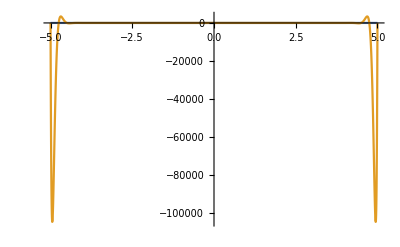

```mathematica
Plot[{f[x],%},{x,-5,5}, PlotRange->All]
```

## Splines

Para evitar estos problemas podemos pensar en polinomios de grados bajos pero unidos unos con otros (funciones polinómicas a trozos). Se llaman splines polinomiales.

El ejemplo más fácil de esto es una poligonal. Serían polinomios de grado menor o igual a 1 unidos con continuidad. 

Ejemplo: Spline lineal

```mathematica
p1[x_]:= a + b x
```

```mathematica
p2[x_]:= c + d x
```

```mathematica
p3[x_]:= e + f x
```

```mathematica
Solve[{p1[0]==9,p1[2]==6},{a,b}]
```

{{a→9,b→-3/2}}

```mathematica
Solve[{p2[2]==6,p2[4]==10},{c,d}]
```

{{c→2,d→2}}

```mathematica
Solve[{p3[4]==10,p3[7]==15},{e,f}]
```

{{e→10/3,f→5/3}}

La función spline se define por trozos, utilizando la función Which:

```mathematica
s[x_]:=Which[0≤x≤2,9-3/2 x,2≤x≤4,2+2x,4≤x≤7,10/3+5/3 x]
```

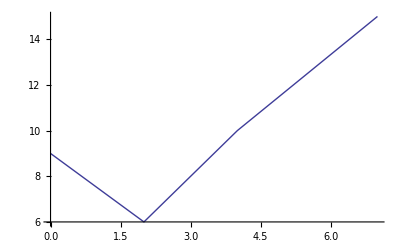

```mathematica
splinelineal=Plot[s[x],{x,0,7}]
```

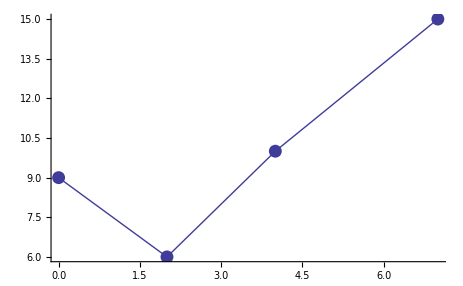

```mathematica
Show[puntos,splinelineal]
```

Podríamos considerar diferentes grados de polinomios y diferentes formas de unión (sólo continuidad, derivabilidad, segunda derivada, etc.). Esto se expresa diciendo que el spline es lineal o cuadrático o cúbico, para referirnos al grado máximo de los polinomios, y de clase 0 (si simplemente unen de forma continua), clase 1 (si los trozos unen con el mismo valor y la misma pendiente), clase 2 (cuando los trozos unen con continuidad de la función, la primera y segunda derivada).  

Un spline bastante útil en la práctica es el cúbico natural. Se trata de un spline cúbico de clase 2. Los polinomios cúbicos enlazan con el mismo valor, misma derivada y misma segunda derivada y además el spline tiene derivada segunda igual a 0 en los extremos del intervalo global.

```mathematica
c1[x_]:=a + b x + c x^2 + d x^3
```

```mathematica
c2[x_]:= e + f x + g x^2 + h x^3
```

```mathematica
c3[x_]:= i + j x + k x^2 + l x^3
```

Imponemos los datos y las condiciones

```mathematica
Solve[{c1[0]==9,c1[2]==6,c2[2]==6,c2[4]==10,c3[4]==10,c3[7]==15,c1'[2]==c2'[2],c1''[2]==c2''[2],c2'[4]==c3'[4],c2''[4]==c3''[4],c1''[0]==0,c3''[7]==0},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{{a→9,b→-139/57,c→0,d→107/456,e→252/19,f→-53/6,g→243/76,h→-17/57,i→-1460/171,j→857/114,k→-203/228,l→29/684}}

```mathematica
{c1[x],c2[x],c3[x]}/.%
```

{{9-(139 x)/57+(107 x^3)/456,252/19-(53 x)/6+(243 x^2)/76-(17 x^3)/57,-1460/171+(857 x)/114-(203 x^2)/228+(29 x^3)/684}}

```mathematica
scn[x_]:=Which[0≤x≤2,9-(139 x)/57+(107 x^3)/456,2≤x≤4,252/19-(53 x)/6+(243 x^2)/76-(17 x^3)/57,4≤x≤7,-1460/171+(857 x)/114-(203 x^2)/228+(29 x^3)/684]
```

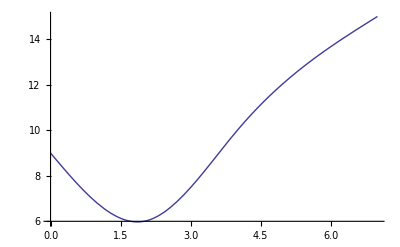

```mathematica
sc=Plot[scn[x],{x,0,7}]
```

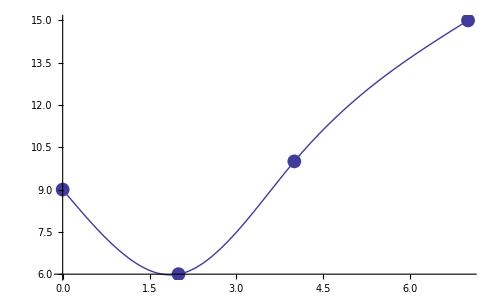

```mathematica
Show[sc,puntos]
```

Utilizando una base de las funciones splines.
Una forma más sencilla de calcular, pues se reduce el número de ecuaciones e incógnitas con las que trabajamos, es utilizar la base de las funciones splines.
En el ejemplo anterior, podríamos escribir la función en el primer intervalo como un polinomio de grado menor o igual a tres, a + b x + c x^2 + d x^3. Al pasar del primer al segundo intervalo, no puede cambiar ni el valor de la función, ni la derivada primera, ni la segunda, por tanto la diferencia entre el polinomio del segundo intervalo y el del primero tiene que ser un polinomio de la forma e (x-2)^3. Análogamente, la diferencia entre el polinomio del tercer intervalo y el del segundo debe ser de la forma f (x-4)^3. Por ello podríamos escribir la función spline de la forma
a + b x + c x^2 + d x^2+ e ((x-2)^3)_++ f ((x-4)^3)_+
Donde la notación ((x-a)^n)_+ significa que la función vale 0 cuando la variable x sea menor que a y vale (x-a)^n cuando x es mayor o igual que a.

```mathematica
base[x_,a_,n_]:= Which[x≥ a, (x-a)^n, x<a, 0]
```

```mathematica
s[x_]:= a + b x + c x^2 + d x^3 + e base[x,2,3]+ f base[x,4,3]
```

```mathematica
Solve[{s[0]==9,s[2]==6,s[4]==10,s[7]==15,s''[0]==0,s''[7]==0},{a,b,c,d,e,f}]
```

{{a→9,b→-139/57,c→0,d→107/456,e→-81/152,f→233/684}}

```mathematica
s[x]/.%
```

{9-(139 x)/57+(107 x^3)/456-81/152 Which[x≥2,(x-2)^3,x<2,0]+233/684 Which[x≥4,(x-4)^3,x<4,0]}

```mathematica
Plot[9-(139 x)/57+(107 x^3)/456-81/152 Which[x≥2,(x-2)^3,x<2,0]+233/684 Which[x≥4,(x-4)^3,x<4,0],{x,0,7}]
```

-Graphics-

### Funciones splines

#### 1) Calcular la poligonal que interpola los datos f(0)=7, f(2)=9, f(3)=6, f(5)=8.

```mathematica
a=ListPlot[{{0,7},{2,9},{3,6},{5,8}},PlotStyle->PointSize[0.04]];
```

```mathematica
s[x_]:=Which[0≤x≤2,7+x,2≤x≤3,9-3(x-2),3≤x≤5,6+(x-3)]
```

```mathematica
b=Plot[s[x],{x,0,5}];
```

```mathematica
Show[a,b];
```

#### 2) Calcular la poligonal del problema 1 utilizando las funciones base de los splines.

```mathematica
Clear[a,b]
```

```mathematica
b[x_,a_,n_]:=Which[x≤a,0,x>a,(x-a)^n]
```

```mathematica
s[x_]:=a0+a1(x-0)+a2 b[x,2,1]+a3 b[x,3,1]
```

```mathematica
Solve[{s[0]==7,s[2]==9,s[3]==6,s[5]==8},{a0,a1,a2,a3}]
```

{{a0→7,a1→1,a2→-4,a3→4}}

```mathematica
s[x]/.%
```

{7+x-4 Which[x≤2,0,x>2,(x-2)^1]+4 Which[x≤3,0,x>3,(x-3)^1]}

```mathematica
D[b[x,3,2],x]/.x->4
```

2

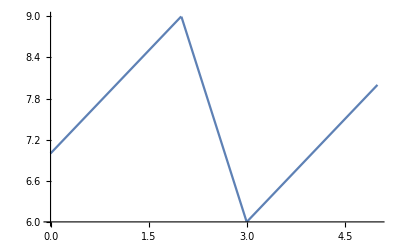

```mathematica
Plot[7+x-4 Which[x≤2,0,x>2,(x-2)^1]+4 Which[x≤3,0,x>3,(x-3)^1],{x,0,5}]
```

### 3) Calcular el spline cuadrático clase 1 que interpola los datos f (2) = 3, f' (2) = m, f (4) = 5, f (8) = 4, f (10) = 0. Usar diferentes valores de m .

```mathematica
a=ListPlot[{{2,3},{4,5},{8,4},{10,0}},PlotStyle->PointSize[0.04]];
```

```mathematica
b[x_,a_,n_]:=Which[x≤a,0,x>a,(x-a)^n]
```

```mathematica
c[x_]:=a0 + a1 x + a2 x^2 + a3 b[x,4,2]+a4 b[x,8,2]
```

```mathematica
Solve[{c[2]==3,c'[2]==m,c[4]==5,c[8]==4,c[10]==0},{a0,a1,a2,a3,a4}]
```

{{a0→5-4 m,a1→-2+3 m,a2→(1-m)/2,a3→1/16 (-17+12 m),a4→1/16 (13-12 m)}}

```mathematica
c[x]/.%
```

{5-4 m+(-2+3 m) x+1/2 (1-m) x^2+1/16 (-17+12 m) Which[x≤4,0,x>4,(x-4)^2]+1/16 (13-12 m) Which[x≤8,0,x>8,(x-8)^2]}

```mathematica
Manipulate[Show[a,Plot[{-3,15,Min[15,Max[-3,3+m(x-2)]],5-4 m+(-2+3 m) x+1/2 (1-m) x^2+1/16 (-17+12 m) Which[x≤4,0,x>4,(x-4)^2]+1/16 (13-12 m) Which[x≤8,0,x>8,(x-8)^2]},{x,2,10}],PlotRange->All],{m,-5,5}]
```

## Ejemplos de aproximación por mínimos cuadrados.

Ejemplo 1. Calcular la recta que mejor aproxima en el sentido de los mínimos cuadrados los datos siguientes: (1,3), (2,5) (3,7), (0,1) , (8,12).

Solución: Las funciones con las que vamos aproximar son las combinaciones lineales de las funciones 1 y x. Una vez que tenemos los datos y las funciones tenemos que definir la función error. Al minimizarla encontramos la solución.

```mathematica
p[x_]:= a*1 + b*x
```

```mathematica
error[a_,b_]:=(p[1]-3)^2+ (p[2]-5)^2+ (p[3]-7)^2+ (p[0]-1)^2+ (p[8]-12)^2
```

```mathematica
error[a,b]
```

(-1+a)^2+(-3+a+b)^2+(-5+a+2 b)^2+(-7+a+3 b)^2+(-12+a+8 b)^2

Para minimizar calculamos las derivadas parciales de este error, las igualamos a cero y resolvemos el sistema.

```mathematica
D[error[a,b],a]
```

2 (-1+a)+2 (-3+a+b)+2 (-5+a+2 b)+2 (-7+a+3 b)+2 (-12+a+8 b)

```mathematica
D[error[a,b],b]
```

2 (-3+a+b)+4 (-5+a+2 b)+6 (-7+a+3 b)+16 (-12+a+8 b)

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→182/97,b→129/97}}

```mathematica
p[x]/.%
```

{182/97+(129 x)/97}

Por tanto, la recta que mejor aproxima en el sentido de los mínimos cuadrados es y=182/97+129/97x.

```mathematica
recta=Plot[%,{x,0,8}];
```

```mathematica
puntos=ListPlot[{{1,3},{2,5},{3,7},{0,1},{8,12}},PlotStyle->PointSize[0.02]];
```

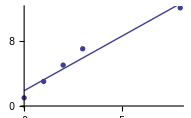

```mathematica
Show[puntos,recta]
```

Ejemplo 2. Calcular la recta que mejor aproxima en el sentido de los mínimos cuadrados los datos siguientes: {(2, 3), (4, 5), (6, 6), (8, 7), (9, 9), (10, 11), (12, 14)}.

Solución:

```mathematica
datos={{2,3},{4,5},{6,6},{8,7},{9,9},{10,11},{12,14},{3,6},{8,10},{4,5},{4.5,6.5}}
```

{{2,3},{4,5},{6,6},{8,7},{9,9},{10,11},{12,14},{3,6},{8,10},{4,5},{4.5,6.5}}

En la lista datos incluimos la información de los puntos (x_i, y_i). Buscamos la función lineal (f(x) = a + b x )  que para los x_i vale lo más parecido posible a y_i.

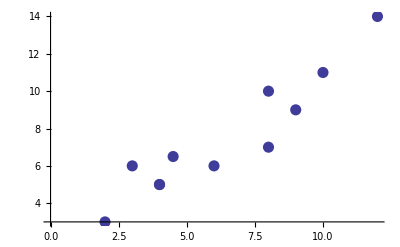

```mathematica
puntos=ListPlot[datos,PlotStyle->PointSize[0.02]]
```

```mathematica
n=Length[datos]
```

11

La función Length cuenta los elementos que hay en la lista. Utilizamos el valor calculado, n, para incluirlo en el sumatorio de los errores. También podemos calcular el mínimo y el máximo de la variable x, para hacer la gráfica posterior.

```mathematica
min=Min[Table[datos[[i]][[1]],{i,1,n}]]
```

2

```mathematica
max=Max[Table[datos[[i]][[1]],{i,1,n}]]
```

12

```mathematica
error[a_,b_]:=∑_(i=1)^n (a +b datos[[i,1]]-datos[[i,2]])^2
```

Para cada x_i, el polinomio a + b x toma un valor. Intentamos que ese valor sea lo más parecido posible a y_i. Las diferencias al cuadrado, sumadas dan lugar a la función error. Derivando esta función encontramos los posibles puntos de máximos o mínimos. Aunque no lo demostraremos, el sistema con las primeras derivadas parciales igualadas a cero tiene una única solución y se corresponderá con un mínimo.

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→1.5233,b→0.932534}}

```mathematica
{a + b x}/.%
```

{{1.5233+0.932534 x}}

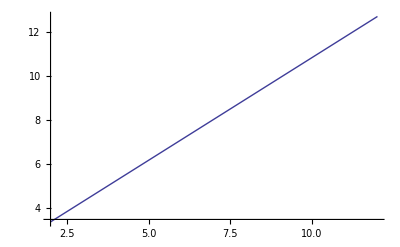

```mathematica
recta=Plot[%,{x,min,max}]
```

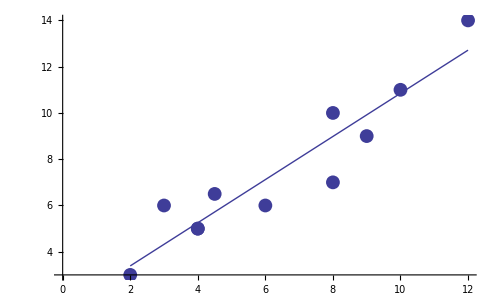

```mathematica
Show[puntos,recta]
```

Ejemplo 3. Calcular la parábola que mejor aproxima en el sentido de los mínimos cuadrados los puntos (1,5), (2,4), (3,4), (5,7), (8, 15), (10, 25).

Solución: Ahora cambian las funciones aproximantes, tenemos que usar combinaciones lineales de las funciones 1, x, x^2.

```mathematica
p[x_]:= a + b x + c x^2
```

```mathematica
datos={{1,5},{2,4},{3,4},{5,7},{8,15},{10,25}}
```

{{1,5},{2,4},{3,4},{5,7},{8,15},{10,25}}

```mathematica
n=Length[datos]
```

6

```mathematica
min=Min[Table[datos[[i]][[1]],{i,1,n}]]
```

1

```mathematica
max=Max[Table[datos[[i]][[1]],{i,1,n}]]
```

10

```mathematica
error[a_,b_,c_]:=∑_(i=1)^n (p[datos[[i,1]]]-datos[[i,2]])^2
```

```mathematica
Solve[{D[error[a,b,c],a]==0,D[error[a,b,c],b]==0,D[error[a,b,c],c]==0},{a,b,c}]
```

{{a→4667/748,b→-15733/8976,c→22717/62832}}

```mathematica
p[x]/.%
```

{4667/748-(15733 x)/8976+(22717 x^2)/62832}

La parábola de mínimos cuadrados es y = 4667/748-(15733 x)/8976+(22717 x^2)/62832.

```mathematica
parabola=Plot[%,{x,min,max}];
```

```mathematica
puntos=ListPlot[datos,PlotStyle->PointSize[0.02]];
```

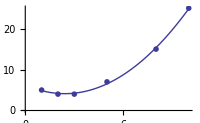

```mathematica
Show[puntos,parabola]
```

Ejemplo 4: Calcular la parábola que mejor aproxima en el sentido de los mínimos cuadrados los puntos (3,4), (5,6), (5,7), (6,7), (8, 10), (12,7), (15,2).

Solución:

```mathematica
datos={{3,4},{5,6},{5,7},{6,7},{8,10},{12,7},{15,2}}
```

{{3,4},{5,6},{5,7},{6,7},{8,10},{12,7},{15,2}}

```mathematica
n=Length[datos]
```

7

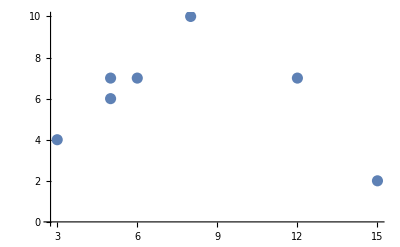

```mathematica
puntos=ListPlot[datos,PlotStyle->PointSize[0.02]]
```

```mathematica
min=Min[Table[datos[[i]][[1]],{i,1,n}]]
```

3

```mathematica
max=Max[Table[datos[[i]][[1]],{i,1,n}]]
```

15

```mathematica
p[x_]:=a + b x + c x^2
```

```mathematica
err[a_,b_,c_]:=∑_(i=1)^Length[datos] (p[datos[[i,1]]]-datos[[i,2]])^2
```

```mathematica
Solve[{D[err[a,b,c],a]==0,D[err[a,b,c],b]==0,D[err[a,b,c],c]==0},{a,b,c}]
```

{{a→-23351/5948,b→107173/35688,c→-6197/35688}}

```mathematica
p[x]/.%
```

{-23351/5948+(107173 x)/35688-(6197 x^2)/35688}

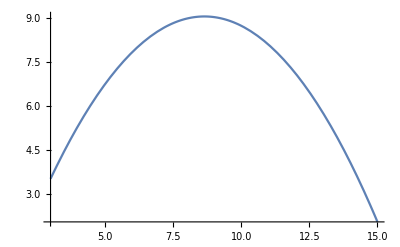

```mathematica
parabola=Plot[%,{x,min,max}]
```

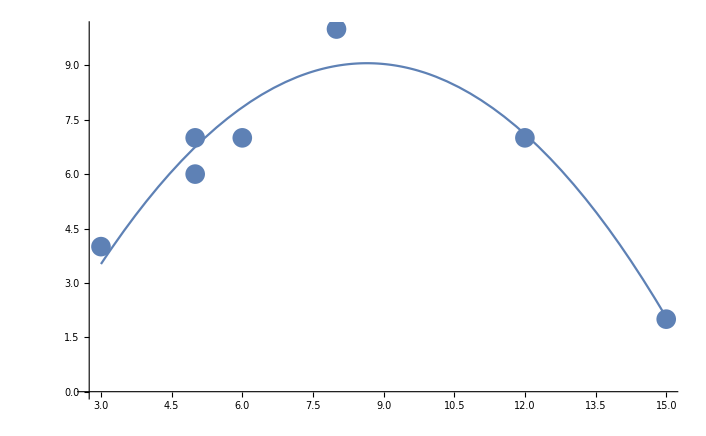

```mathematica
Show[puntos,parabola]
```

En general, podemos considerar combinaciones lineales de funciones ( por ejemplo: a + b x + c x^2+ d x^3+ e x^4, a + b cos x + c sen x, a + b x + c cos x + d ⅇ^x, ..., ),  definir la función suma de errores al cuadrado, calcular derivadas parciales, igualarlas a cero y resolver el sistema.

Ejemplo 5. Calcular la combinación lineal de las funciones 1, cos x, e^x que mejor aproxima en el sentido de los mínimos cuadrados los puntos (1,5), (2,4), (3,4), (5,7), (8, 15), (10, 25).

Solución: Ahora cambian las funciones aproximantes, tenemos que usar combinaciones lineales de las funciones 1, cos x, e^x.

```mathematica
p[x_]:= a + b Cos[x] + c ⅇ^x
```

```mathematica
datos={{1,5},{2,4},{3,4},{5,7},{8,15},{10,25}}
```

{{1,5},{2,4},{3,4},{5,7},{8,15},{10,25}}

```mathematica
n=Length[datos]
```

6

```mathematica
min=Min[Table[datos[[i]][[1]],{i,1,n}]]
```

1

```mathematica
max=Max[Table[datos[[i]][[1]],{i,1,n}]]
```

10

```mathematica
error[a_,b_,c_]:=∑_(i=1)^n (p[datos[[i,1]]]-datos[[i,2]])^2
```

```mathematica
Solve[{D[error[a,b,c],a]==0,D[error[a,b,c],b]==0,D[error[a,b,c],c]==0},{a,b,c}]//N
```

{{a→6.49521,b→1.72547,c→0.000942273}}

```mathematica
p[x]/.%
```

{6.49521+0.000942273 ⅇ^x+1.72547 Cos[x]}

La función es y = 6.49521+0.000942273 ⅇ^x+1.72547 Cos[x].

```mathematica
aproximante=Plot[%,{x,min,max},PlotRange->All];
```

```mathematica
puntos=ListPlot[datos,PlotStyle->PointSize[0.02]];
```

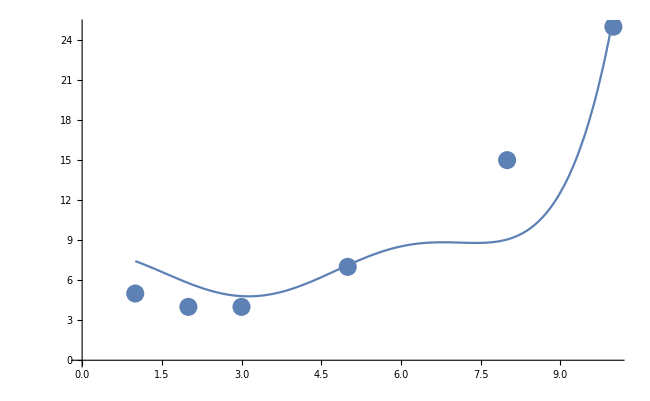

```mathematica
Show[puntos,aproximante]
```